This Notebook is made only for cases near tunnelling-without-barrier scenarios, that is, ω+2ω fields with π/2 phase shift and equal intensities.

## Configurations and Equations

### Field Configuration

#### Unit conversions

```mathematica
λToω[λ_]:=2π (0.052918 ×137)/λ
```

```mathematica
ωToλ[ω_]:=2π (0.052918 ×137)/ω
```

#### fieldConfig struct

```mathematica
fieldConfig::usage = "fieldConfig[] is a protected variable, which will act to hold an association of all its defining components, e.g., the time-dependence, wavelength, intensity";
Protect[fieldConfig];
(*this is the container (struct) where I can put all the field information into*)
```

```mathematica
fcSymbolic=fieldConfig["E1"->E1,"E2"->E2,"E0"->E0,"ϕ1"->ϕ1,"ϕ2"->ϕ2,"r"->1,"s"->2,"ω"->ω];
fcSymbolicToStrings={E1->"E1",E2->"E2",E0->"E0",ϕ1->"ϕ1",ϕ2->"ϕ2",ω->"ω"};
```

#### TWOBfcSymbolic (the tunnelling without barrier scenario)

```mathematica
TWOBfcSymbolic=makeFieldConfig["θ"->π/4,
"E0"->E0,
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->ω]
```

#### makeFieldConfig

```mathematica
makeFieldConfig["E1"->E1_,"E2"->E2_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_]:=fieldConfig[
"E1"->E1,
"E2"->E2,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,
"ω"->ω]
(* this shall generate a fieldConfig that can then be used for further computation of the field, the potential, the action etc. *)
```

I can overload this with a lot of definitions, e.g. income intensity etc.

```mathematica
makeFieldConfig["θ"->θ_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_]:=fieldConfig[
"E1"->Cos[θ]E0,
"E2"->Sin[θ]E0,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,
"ω"->ω]
```

A tunnelling-without-barrier scenario will (at least for now) always be this:

```mathematica
makeTWOBFieldConfig["E0"->E0_,"ω"->ω_]:=makeFieldConfig["θ"->π/4,
"E0"->E0,
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->ω]
```

#### test configuration

```mathematica
testfieldconfig=makeFieldConfig["θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800]]
```

fieldConfig[E1→0.0755929,E2→0.0755929,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395]

### Target Configuration

```mathematica
targetConfig::usage = "targetConfig is a protected variable, which will hold the value for the ionization potential (as this is the only defining quantity for now)";
Protect[targetConfig];
```

#### κFromConfig

```mathematica
κFromConfig[targetConfig_]:= √(2 "Ip")/.(Association@@targetConfig)
```

#### Test target

```mathematica
testtargetconfig=targetConfig["Ip"->0.5] (*Hydrogen*)
```

targetConfig[Ip→0.5]

#### tcSymbolic

```mathematica
tcSymbolic=targetConfig["Ip"->Ip]
```

targetConfig[Ip→Ip]

### Field equation, vector potential and action

#### Field

```mathematica
fieldFromConfig[fieldConfig_][ωt_]:=Module[{f,fun},
f=Association@@fieldConfig;
"E1" "E0" Sin["r" ωt + "ϕ1"]+"E2" "E0" Sin["s" ωt+"ϕ2"]/.f
]
```

```mathematica
fieldFromConfig[TWOBfcSymbolic][ωt]
```

(E0^2 Cos[ωt])/(√2)-(E0^2 Cos[2 ωt])/(√2)

#### Potential

```mathematica
potential[ωt_]:=Module[{f,fun,field,pot,intfactor},
field=fieldFromConfig[fcSymbolic][ωt];
-1/ω×Integrate[field,ωt]//Simplify
]
```

```mathematica
potentialFromConfig::usage="potentialFromConfig[fieldConfig] takes in a valid fieldConfig object and returns a vector potential A as a Function object, where A[t] is a numeric (or symbolic) vector potential";
potentialFromConfig[fieldConfig_][ωt_]:=Module[{f,fun,field,pot,intfactor},
f=Association@@fieldConfig;
potential[ωt]/.fcSymbolicToStrings/.f
]
```

#### Action

```mathematica
action[p_,ωt_]=Module[{f,fun,field,pot,IntPot,IntPotsq},
field=fieldFromConfig[fcSymbolic][ωt];
pot=potentialFromConfig[fcSymbolic][ωt];
IntPot=Integrate[pot,ωt];
IntPotsq=Integrate[pot*pot,ωt];

(1/2 (p^2 ωt +2 p IntPot+IntPotsq) +1/2 κ^2 ωt)
]
```

(κ^2 ωt)/2+1/2 (p^2 ωt+2 p ((E0 E1 Cos[ωt] Sin[ϕ1])/ω+(E0 E2 Cos[2 ωt] Sin[ϕ2])/(4 ω)+(E0 E1 Cos[ϕ1] Sin[ωt])/ω+(E0 E2 Cos[ϕ2] Sin[2 ωt])/(4 ω))+(E0^2 (2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ϕ1-ϕ2-ωt]+E1^2 Sin[2 (ϕ1+ωt)]+1/8 E2^2 Sin[2 (ϕ2+2 ωt)]+2/3 E1 E2 Sin[ϕ1+ϕ2+3 ωt]))/(4 ω^2))

```mathematica
actionFromConfig[fieldConfig_,targetConfig_][p_,ωt_]:=
(*actionFromConfig[fieldConfig,targetConfig][p,ωt]=*)
Module[{f,fun,field,pot,IntPot,IntPotsq},
f=Association@@fieldConfig;

action[p,ωt]/.fcSymbolicToStrings/.f/.κ->κFromConfig[targetConfig]

]
```

```mathematica
actionFromConfig[TWOBfcSymbolic,tcSymbolic][p,ωt]//FullSimplify
```

(60 E0^4 ωt+192 (2 Ip+p^2) ω^2 ωt-48 √2 E0^2 p ω (-4 Cos[ωt]+Cos[2 ωt])-E0^4 (48 Sin[ωt]+24 Sin[2 ωt]-16 Sin[3 ωt]+3 Sin[4 ωt]))/(384 ω^2)

### Derivatives of the action

#### First derivative

```mathematica
dSdωt[fieldConfig_,targetConfig_][p_,ωt_]:=
(*dSdωt[fieldConfig,targetConfig][p,ωt]=*)
Module[{drv,px},
drv[px_,x_]=D[actionFromConfig[fieldConfig,targetConfig][px,x],x];

Function[{px,x},
drv[px,x]
][p,ωt]

]
```

#### Second derivative

```mathematica
d2Sdωt2[fieldConfig_,targetConfig_][p_,ωt_]:=Module[{drv2,px},
drv2[px_,x_]=D[actionFromConfig[fieldConfig,targetConfig][px,x],{x,2}];

Function[{px,x},
drv2[px,x]
][p,ωt]

]
```

### Derived quantities about the setup

#### Keldysh parameter

```mathematica
KeldyshγFromConfig[fieldConfig_,targetConfig_]:=Sqrt[("Ip"/.(Association@@targetConfig))/(2 UpondFromConfig[fieldConfig])]
```

```mathematica
KeldyshγFromConfig[fieldConfig_,targetConfig_,"Upfixed"]:=Sqrt[("Ip"/.(Association@@targetConfig))/(2 (("E0")/("ω"))^2/.(Association@@fieldConfig))]
```

```mathematica
KeldyshγFromConfig[testfieldconfig,testtargetconfig]
```

1.77245 √(1/(∫_0^(2 π) (potentialFromConfig[fieldConfig[E1→0.0755929,E2→0.0755929,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395]][ωt])^2 ⅆωt))

#### ponderomotive energy (Upond)

```mathematica
UpondFromConfig[fieldConfig_]:=5/32(("E0")/("ω"))^2/.(Association@@fieldConfig);
```

#### Strong-field parameter

```mathematica
zfFromConfig[fieldConfig_]:=("E0")^2/("ω")^3/.(Association@@fieldConfig)
```

```mathematica
zfFromConfig[fieldConfig_,"Updirect"]:=UpondFromConfig[fieldConfig]/("ω")/.(Association@@fieldConfig)
```

```mathematica
zfFromConfig[testfieldconfig]
```

61.9085

## Saddle points

### Utilities for the saddle point search

#### findωtBorder[]: Finding the border between the two bands

```mathematica
findωtBorder[fieldConfig_]:=
Module[{borderrange,bordertime,zeros},
borderrange={π/2,(3π)/4};
zeros=Select[ωt/.
Quiet@NSolve[
fieldFromConfig[fieldConfig][ωt]
==0,ωt]/.C[1]->{0,1}//Flatten
, Abs[Im[#]]<10^-5&];
bordertime=Select[zeros, borderrange[[1]]<=Re[Round[#,10^-5]]<=borderrange[[2]]&][[1]];
Return[bordertime]
]
```

#### Grid of seeds

```mathematica
SeedsGrid[fieldConfig_]:=Module[{},
(*Print[fieldConfig];*)
Flatten[Table[
ωtreal0+ⅈ ωtimag0,
{ωtreal0,-π,7/5 π,1},
{ωtimag0,0,If[(Association@@fieldConfig)[["E1"]]!=0 && (*I added this bc I don't want to divide by zero. I think it's not the best way to do it though*)
((Association@@fieldConfig)[["E2"]])/((Association@@fieldConfig)[["E1"]])<0.1,5π,6/5 π],0.5}
],1]
]
```

### Finding saddle points

#### findSaddles[]

```mathematica
findSaddles::usage="findSaddles[fieldConfig_,targetConfig_][px_] searches for solutions of the first derivative of the action within -π and 2π. It return a list of phase values, ordered by their real part, which can then be sorted by the classification functions";
findSaddles[fieldConfig_,targetConfig_][px_]:=
Module[{allsolutions,solutions,seeds,ωtmin},
seeds=SeedsGrid[fieldConfig];
allsolutions = Block[{},Table[ωtx/.
Quiet@FindRoot[
dSdωt[fieldConfig,targetConfig][px,ωtx]==0,
{ωtx,ωtSeed}],
{ωtSeed,seeds}
]];
DeleteCases[solutions,{}];
solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
solutions=Select[solutions,Abs[dSdωt[fieldConfig,targetConfig][px,#]]<10^-5&];

solutions=Select[solutions,And[Im[#]>0,-π<=Re[#]<2π]&];
(*Print[solutions];*)
solutions=SortBy[solutions,Re[#]&];
Return[solutions]
]
```

```mathematica
findSaddles[testfieldconfig,testtargetconfig][0.1]//AbsoluteTiming
```

{0.197548,{-1.32697+1.6852 ⅈ,-0.0411638+1.85431 ⅈ,1.42544+1.66456 ⅈ,3.08429+1.49545 ⅈ}}

#### Plotting fields and saddles

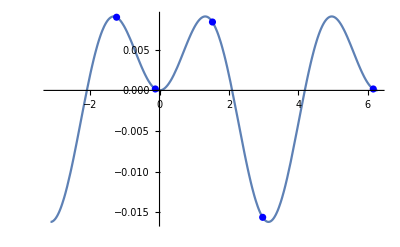

```mathematica
Block[{px=0.3, fc=testfieldconfig, saddles, tc=testtargetconfig},
saddles=findSaddles[fc,tc][px];
Show[{
Plot[fieldFromConfig[fc][ωt],{ωt,-π,2π}],
ListPlot[{Re[#],fieldFromConfig[fc][Re[#]]}&/@saddles,PlotStyle->Blue]
(*,ListPlot[{Re[#],fieldFromConfig[testfieldconfig1][Re[#]]}&/@findSaddles[testfieldconfig1,testtargetconfig][4],PlotStyle->Red]*)
}]
]
```

```mathematica
DynamicModule[{fc=testfieldconfig, saddles, tc=testtargetconfig},
Manipulate[
saddles=findSaddles[fc,tc][px];
Show[{
Plot[fieldFromConfig[fc][ωt],{ωt,-π,2π}],
ListPlot[{Re[#],fieldFromConfig[fc][Re[#]]}&/@saddles,PlotStyle->Blue]
}]
,{px,-3,+3}]
]
```

ListPlot::lpn: findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E0→0.106904,ϕ1→1.5708,ϕ2→-1.5708,r→1.,s→2.,ω→0.0569395],targetConfig[Ip→0.5]][{2.88,fieldFromConfig[fieldConfig[«1»]][«18»]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{,ListPlot[findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395],targetConfig[Ip→0.5]][{2.88,fieldFromConfig[fieldConfig[Rule[«2»],«6»,Rule[«2»]]][«18»]}],«9»→color]}].

ListPlot::lpn: findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E0→0.106904,ϕ1→1.5708,ϕ2→-1.5708,r→1.,s→2.,ω→0.0569395],targetConfig[Ip→0.5]][{2.88,fieldFromConfig[fieldConfig[«1»]][«18»]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{,ListPlot[findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395],targetConfig[Ip→0.5]][{2.88,fieldFromConfig[fieldConfig[Rule[«2»],«6»,Rule[«2»]]][«18»]}],«9»→color]}].

### Classifying saddle points

#### ClassifySaddles[]

```mathematica
classifySaddles[fieldConfig_,targetConfig_][saddlesList_]:=Module[{
saddles,
ABCsaddles,
ABCsaddlesclassified,Dsaddle,
classifiedsaddles,
ωtmin,ωtborder,nsaddles1cycle,
myπ
},

ωtborder=findωtBorder[fieldConfig];

saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];

nsaddles1cycle=Length[
Select[saddles,-π<Re[#]<=π&]
];

(*Print["nsaddles1cycle: ",nsaddles1cycle];*)

Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{ACsaddles},
ABCsaddles=SortBy[saddles[[1;;3]],Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];
(*Print["ACSaddles: ",ACsaddles];*)
ABCsaddlesclassified= Join[
{{ABCsaddles[[3]],"B"}},
{{ACsaddles[[1]],"A"}},
{{ACsaddles[[2]],"C"}} 
]

],

nsaddles1cycle<3,
Print["You're trying to classifying less than three saddle points, who knows how to do that!?!"];
,

nsaddles1cycle==3,
ABCsaddlesclassified={
{saddles[[1]],"A"},{saddles[[1]],"C"},
{saddles[[2]],"B"} }

];

Dsaddle=Select[saddles[[Min[nsaddles1cycle,4];;-1]],ωtborder<Re[#]&][[1]];

classifiedsaddles=SortBy[
Join[
ABCsaddlesclassified,
{{Dsaddle,"D"}}
],Re[#[[1]]]&]
]
```

```mathematica
Block[{px=0.3, fc=testfieldconfig, saddles, tc=testtargetconfig},
saddles=findSaddles[fc,tc][px];
classifySaddles[fc,tc][saddles]
]
```

{{-1.23811+1.72271 ⅈ,A},{-0.120844+1.86866 ⅈ,B},{1.52644+1.66391 ⅈ,C},{2.9741+1.51796 ⅈ,D}}

#### Colors for labels

```mathematica
LabelColors=<|"A"->Lighter[RGBColor[0.92, 0.16, 0.05],0.15],"B"->RGBColor[0, 0.9, 0.13],"C"->Darker[RGBColor[0, 0.4, 0.875],0.15],"D"->RGBColor[1, 0.9, 0]|>
```

<|A→RGBColor[0.932, 0.28600000000000003, 0.1925],B→RGBColor[0, 0.9, 0.13],C→RGBColor[0., 0.34, 0.74375],D→RGBColor[1, 0.9, 0]|>

### Checking which saddles are relevant

#### actionsForSaddles[]

```mathematica
actionsForSaddles[fieldConfig_,targetConfig_][px_]:=
Association[
Apply[
Function[{ωt,label},label->actionFromConfig[fieldConfig,targetConfig][px,ωt]],
classifySaddles[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][px]] 
,{1}
]]
```

```mathematica
actionsForSaddles[testfieldconfig,testtargetconfig][0.3]
```

<|A→-0.543247+0.821811 ⅈ,B→-0.080881+0.893726 ⅈ,C→0.876923+0.719744 ⅈ,D→1.52173+0.647829 ⅈ|>

#### contributingSaddles[]

```mathematica
contributingSaddles[fieldConfig_,targetConfig_][px_]:=
Module[{actions,myfun},
actions=actionsForSaddles[fieldConfig,targetConfig][px];
myfun=Function[x,Abs[Re[Round[x,10^-5]]]];
(*THIS IS NOT YET CORRECT THOUGHT THROUGH*)
Which[px>0,
Which[
myfun[actions[["C"]]]<myfun[actions[["A"]]],
{"C","D"},
myfun[actions[["C"]]]<myfun[actions[["B"]]],
{"C","B","D"},
myfun[actions[["A"]]]==myfun[actions[["B"]]]==myfun[actions[["C"]]],
{"A","D"},
True,
{"A","B","C","D"}
],
px<0,
Which[
myfun[actions[["A"]]]<myfun[actions[["C"]]],
{"A","D"},
myfun[actions[["A"]]]<myfun[actions[["B"]]],
{"A","B","D"},
myfun[actions[["A"]]]==myfun[actions[["B"]]]==myfun[actions[["C"]]],
{"A","D"},
True,
{"A","B","C","D"}
],
px==0,
Which[
myfun[actions[["A"]]]==myfun[actions[["B"]]]==myfun[actions[["C"]]],
{"A","D"},
True,
{"A","B","C","D"}
],
True,
Print["I think I've got a mistake here"]
]

]
```

```mathematica
contributingSaddles[testfieldconfig,testtargetconfig][3.]//AbsoluteTiming
```

{0.106574,{A,B,C,D}}

## Ionization Yield

### Yield for one single saddle point

#### yield[]

From equation (53) in J Phys 2014 Popruzhenko

```mathematica
yield[fieldConfig_,targetConfig_][saddle_Association]:=Block[{ωtx,ω,px,κ},
{ωtx,px}={#["ωt"],#["p"]}&@saddle;
 ω="ω"/.(Association@@fieldConfig);
κ=κFromConfig[targetConfig];
(
1/2 Sqrt[ (ⅈ κ)/(d2Sdωt2[fieldConfig,targetConfig][px,ωtx] ω)] 
×Ckl × Ylm
×Exp[ⅈ actionFromConfig[fieldConfig,targetConfig][px,ωtx]/ω ]
)/.{Ckl->1, Ylm->Sqrt[1/(4π)]}  (*Ckl is a dimensionless asymptotic and can be taken to be 1 for Hydrogen*)

]
```

```mathematica
SphericalHarmonicY[0,0,theta,r]
```

1/(2 √π)

p = potA[ωt0] : drift momentum (measured at the detector), for non-zero velocity at ionization, use: p=potA[ωt0] +v0

### for a given p, get all saddles’ yields

```mathematica
yieldsPerSaddles[fieldConfig_,targetConfig_][px_]:=Module[{saddles,data,contributors},
(*find and classify saddles*)
saddles=<|"label"->#[[2]],"p"->px,"ωt"->#[[1]]|>&/@classifySaddles[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][px]];
(*add each saddles' contribution to that dictionary*)
data=Append[#,"yield"->Quiet@yield[fieldConfig,targetConfig][#]]&/@saddles;
(*check which saddles are contributing and add that info to the dictionary as well*)
contributors=contributingSaddles[fieldConfig,targetConfig][px];
SortBy[(Append[#,"contributing"->MemberQ[contributors,#["label"]]]&/@data),#[["label"]]&]
]
```

```mathematica
yieldsPerSaddles[testfieldconfig,testtargetconfig][0.5]
```

{<|label→A,p→0.5,ωt→-1.16273+1.7713 ⅈ,yield→-1.65609×10^-8-1.0656×10^-8 ⅈ,contributing→True|>,<|label→B,p→0.5,ωt→-0.193553+1.89477 ⅈ,yield→-6.49415×10^-9-2.65414×10^-9 ⅈ,contributing→True|>,<|label→C,p→0.5,ωt→1.6224+1.68205 ⅈ,yield→3.61223×10^-7+2.84325×10^-7 ⅈ,contributing→True|>,<|label→D,p→0.5,ωt→2.87548+1.55857 ⅈ,yield→-1.24894×10^-6+1.15913×10^-7 ⅈ,contributing→True|>}

### Summing contributions from contributing saddles

```mathematica
totalYield[yieldsS_List]:=Total[#["yield"]&/@Select[yieldsS,#["contributing"]&]]
```

## Test: Calculate a whole spectrum (for a given fieldconfig and targetconfig)

#### 0) Define your field configuration and target configuration

for example this:

```mathematica
fcTWOB=makeTWOBFieldConfig["E0"->Sqrt[4×10^14/(3.5×10^16)],(*4×10^14 is the intensity in W/cm^2*)
"ω"->λToω[800]](*800 nm wavelength*)
```

fieldConfig[E1→0.0755929,E2→0.0755929,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395]

```mathematica
target=targetConfig["Ip"->0.5];
```

#### 1) Define pvalues

Note: What is a good range for the values of momentum?

```mathematica
pvalues=Range[-3,3,0.01];
```

#### 2) Get data (this might take a bit)

Tipp #1: use ParallelTable instead Table once you’re sure the code works.
Tipp #2: In case it goes wrong, abort calculations with “Alt” + ”.”

```mathematica
spectrumdata=Block[{fc=fcTWOB,tc=target},
Table[yieldsPerSaddles[fc,tc][px],{px,pvalues}]
]
```

{{<|label→A,p→-3.,ωt→-2.10957+2.18151 ⅈ,yield→-1.94322×10^-53-1.29713×10^-53 ⅈ,contributing→True|>,<|label→B,p→-3.,ωt→0.563723+2.33115 ⅈ,yield→1.10126×10^-67-1.40748×10^-67 ⅈ,contributing→True|>,<|label→C,p→-3.,ωt→0.860905+2.30802 ⅈ,yield→1.90978×10^-67-8.21909×10^-68 ⅈ,contributing→True|>,<|label→D,p→-3.,ωt→3.82654+2.15838 ⅈ,yield→-2.03197×10^-53+1.79083×10^-53 ⅈ,contributing→True|>},599,{1}}
 |  |  |  |

#### 3) Calculate the total yield (i.e., summing over all contributions)

```mathematica
totalspectrumdata=Table[<|"p"->pvalues[[i]],"totalYield"->totalYield[spectrumdata[[i]]]|>,{i,1, Length@pvalues}];
```

#### 4) Plotting the spectrum and each individual contribution

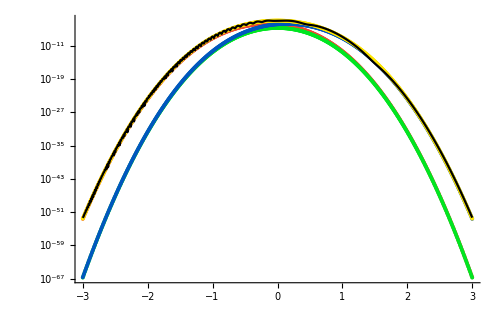

```mathematica
Block[{datalabel},
Show[{
Table[ (*for each label*)
(*extract the data for the respective label from the list*)
datalabel=Function[datap,Select[datap,#["label"]==label &]]/@spectrumdata;

ListLogPlot[{#[[1]]["p"],Abs[#[[1]]["yield"]]}&/@ (*plot (p,yield)*)
datalabel, 
PlotStyle->Directive[LabelColors[label],Thick],Joined->False]

,{label,{"A","B","C","D"}}],

(*plot the total yield as well*)
ListLogPlot[{#["p"],Abs[#["totalYield"]]}&/@totalspectrumdata,PlotStyle->Black,Joined->True]
}
,ImageSize->500
,AxesOrigin->{0,Log[0.001]}
,PlotRange->{Automatic,{Log[10^-30],Automatic}}
]]
```